```mathematica
sub={"abbbb"->"c", "aac"->"c", "cbb"->"c","aaaa"->"aaab", "a"->"aa","b"->"bb" }
```

{abbbb→c,aac→c,cbb→c,aaaa→aaab,a→aa,b→bb}

```mathematica
SubstitutionSystem[sub, "a", 10]
```

{a,aa,aaaa,aaab,aaaaaabb,aaabaaaabbbb,aaaaaabbaaabbbbbbbbb,aaabaaaabbbbaaaacbbbbbbbbbb,aaaaaabbaaabbbbbbbbbaaabcbbbbbbbbbbbbbbbb,aaabaaaabbbbaaaacbbbbbbbbbbaaaaaabbcbbbbbbbbbbbbbbbbbbbbbbbbbbbb,aaaaaabbaaabbbbbbbbbaaabcbbbbbbbbbbbbbbbbaaabaaaabbbbcbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbbb}

```mathematica
sscp=ResourceFunction["SubstitutionSystemCausalPlot"]
```

```mathematica
sscp[SubstitutionSystem[sub, "a", 10]]
```

```mathematica
evo=BlockRandom[SeedRandom[2635];ResourceFunction["SubstitutionSystemCausalEvolution"][sub,"a",20,{"Random",4}]]
```

{{a},{aa,{{1,1}→{1,2}}},{aaaa,{{1,1}→{1,2},{2,2}→{3,4}}},{aaaaaaa,{{2,2}→{2,3},{3,3}→{4,5},{4,4}→{6,7}}},{aaaaaaaaa,{{2,2}→{2,3},{6,6}→{7,8}}},{aaaaaaaaaab,{{1,1}→{1,2},{5,5}→{6,7},{6,9}→{8,11}}},{aaabaaaabaab,{{1,4}→{1,4},{6,9}→{6,9},{10,10}→{10,11}}},{aaaabbaaaabaaaab,{{3,3}→{3,4},{4,4}→{5,6},{10,10}→{12,13},{11,11}→{14,15}}},{aaaabbaaaaaabbaaaaab,{{8,8}→{8,9},{10,10}→{11,12},{11,11}→{13,14},{15,15}→{18,19}}},{aaaaabbaaaaaabbaaaaaaaab,{{1,1}→{1,2},{15,15}→{16,17},{17,17}→{19,20},{18,18}→{21,22}}},{aaaaaabbaaaaaaaabbaaaaabaab,{{2,2}→{2,3},{10,10}→{11,12},{12,12}→{14,15},{18,21}→{21,24}}},{aaaaaaabbaaaaaaaaabbbaaaaabaab,{{4,4}→{4,5},{12,12}→{13,14},{18,18}→{20,21}}},{aaaaaabbbaaaaaaaaaaabbbaaaaaabaab,{{4,7}→{4,7},{17,17}→{17,18},{18,18}→{19,20},{24,24}→{26,27}}},{aaaaaaabbbbaaaaaaaaaaabbbbaaaaaabbaab,{{2,2}→{2,3},{7,7}→{8,9},{21,21}→{23,24},{30,30}→{33,34}}},{aaaaaaaabbbbaaaabaaaaaabbbbaaaababbaab,{{3,3}→{3,4},{13,16}→{14,17},{28,31}→{29,32}}},{aaaaaaaacaaaabaaaaaacaaaababbaab,{{6,6}→{6,7},{8,12}→{9,9},{20,20}→{17,18},{23,27}→{21,21}}},{aaaaaabaacaaaabaaaaaaaacaaaababbaab,{{1,1}→{1,2},{3,6}→{4,7},{15,15}→{16,17},{19,19}→{21,22}}},{aaaababaaacaaaabaaaaabaacaaaababbaab,{{2,5}→{2,5},{8,8}→{8,9},{18,21}→{19,22}}},{aaaaababaaacaaabbaaababaaacaaaababbaab,{{1,1}→{1,2},{12,15}→{13,16},{17,20}→{18,21},{24,24}→{25,26}}},{aaaaaababaaacaaabbaaaababaaaacaaaababbaab,{{4,4}→{4,5},{20,20}→{21,22},{25,25}→{27,28}}},{aaaaaaabaabaaacaaabbaaabbabaaaacaaaaababbaab,{{1,1}→{1,2},{8,8}→{9,10},{19,22}→{21,24},{34,34}→{36,37}}}}

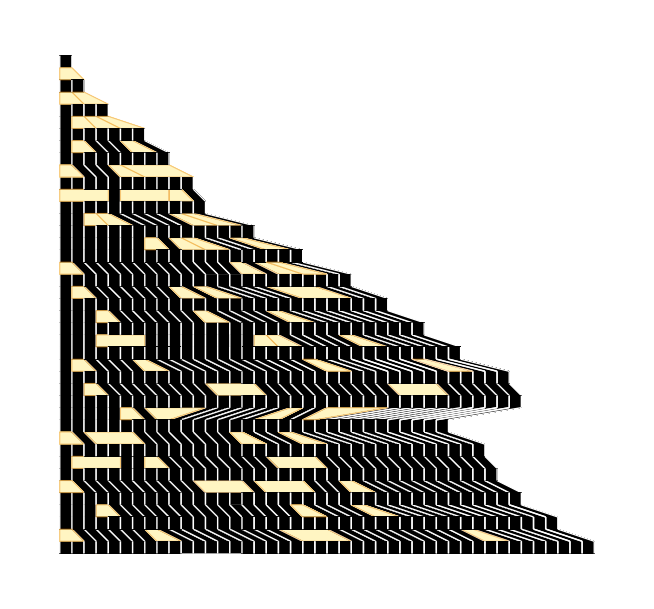

```mathematica
sscp[evo]
```

Sexual reproduction vs asexual? 
Reproduction after a long life (i.e. slow self-replication)?